```mathematica
f=E^(Sin[x])
```

ⅇ^Sin[x]

```mathematica
D[f,x]
```

ⅇ^Sin[x] Cos[x]

```mathematica
g=2^(x^2)
```

2^(x^2)

```mathematica
D[g,x]
```

2^(1+x^2) x Log[2]

```mathematica
Simplify[1/L*Integrate[Sign[x]*x^2*Sin[(n*Pi*x)/L],{x,-L,L}]]
```

-(2 L^2 Sign[L] (2+(-2+n^2 π^2) Cos[n π]-2 n π Sin[n π]))/(n^3 π^3)

```mathematica
(1/L*Integrate[-x^2*Sin[(n*Pi*x)/L],{x,-L,0}])+1/L*Integrate[x^2*Sin[(n*Pi*x)/L],{x,0,L}]
```

-(L^2 (2+(-2+n^2 π^2) Cos[n π]-2 n π Sin[n π]))/(n^3 π^3)+(L^2 (-2+(2-n^2 π^2) Cos[n π]+2 n π Sin[n π]))/(n^3 π^3)

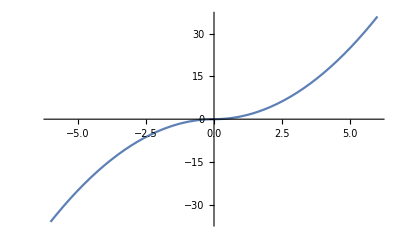

```mathematica
Plot[Sign[x]*x^2,{x,-6,6}]
```